```mathematica
γ[β_]:=1/(√(1-β^2))
```

```mathematica
P[μ_,β_]:=1/(γ[β]^4(1-β μ)^4);
```

```mathematica
Plot[P[μ,0.5],{μ,0,1}];
```

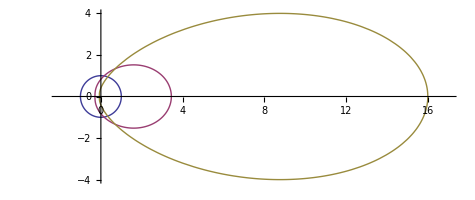

```mathematica
PolarPlot[{P[Cos[θ],0.0],P[Cos[θ],0.3],P[Cos[θ],0.6]},{θ,0,2π},PlotRange->{{-2,17},{-4,4}}]
```